# Potentials: HO, LJ, and M

Author1, Author2, A
School of Physical Sciences and Nanotechnology
Date of Submission

## The harmonic oscillator

We are going to solve analytically the Schrödinger equation for the harmonic oscillator (HO): ℏ , ϕ, ℰ  is esc+scE+esc,

```mathematica
eq = -ℏ^2/(2m) ϕ''[x] + 1/2 m ω^2 x^2 ϕ[x]==ℰ ϕ[x]
```

1/2 m x^2 ω^2 ϕ[x]-(ℏ^2 ϕ''[x])/(2 m)==ℰ ϕ[x]

```mathematica
DSolve[eq,ϕ[x],x]//FunctionExpand//FullSimplify//ExpandAll
```

{{ϕ[x]→2^(1/4+ℰ/(2 ω ℏ)) ⅇ^((m x^2 ω)/(2 ℏ)) C[2] HermiteH[-1/2-ℰ/(ω ℏ),(ⅈ √m x √ω)/(√ℏ)]+2^(1/4-ℰ/(2 ω ℏ)) ⅇ^(-(m x^2 ω)/(2 ℏ)) C[1] HermiteH[-1/2+ℰ/(ω ℏ),(√m x √ω)/(√ℏ)]}}

Let’s check the asymptotic behaviour for ϕ[x⟶∞] and ϕ[x⟶-∞]

```mathematica
Asymptotic[ ⅇ^(-(m x^2 ω)/(2 ℏ)) HermiteH[-1/2+ℰ/(ω ℏ),(√m x √ω)/(√ℏ)],x->∞]//FullSimplify
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) x^(-1/2-ℰ/(ω ℏ)) ((m ω)/ℏ)^(-3/4-ℰ/(2 ω ℏ)) Cos[(π ℰ)/(ω ℏ)] (2^(-1/2+ℰ/(ω ℏ)) √m x^((2 ℰ)/(ω ℏ)) √ω (-(m^2 ω^2)/ℏ^2)^(-1/4+ℰ/(2 ω ℏ)) (√m √ω Csc[1/4 π (1-(2 ℰ)/(ω ℏ))]+√(-(m ω)/ℏ) √ℏ Csc[1/4 π (1+(2 ℰ)/(ω ℏ))])+(ⅇ^((m x^2 ω)/ℏ) (-√m √ω+√((m ω)/ℏ) √ℏ) √ℏ Gamma[1/2+ℰ/(ω ℏ)])/(√π)))/(2 ℏ)

```mathematica
Asymptotic[ ⅇ^(-(m x^2 ω)/(2 ℏ)) HermiteH[-1/2+ℰ/(ω ℏ),(√m x √ω)/(√ℏ)],x->-∞]//FullSimplify
```

(ⅈ ⅇ^(-(2 ⅈ π ℰ+m x^2 ω^2)/(2 ω ℏ)) (1/x)^(1/2-ℰ/(ω ℏ)) ((m ω)/ℏ)^(-3/4-ℰ/(2 ω ℏ)) Cos[(π ℰ)/(ω ℏ)] (2^(-1/2+ℰ/(ω ℏ)) ⅇ^((2 ⅈ π ℰ)/(ω ℏ)) √m √ω (-(m^2 ω^2)/ℏ^2)^(-1/4+ℰ/(2 ω ℏ)) (√m √ω Csc[1/4 π (-1+(2 ℰ)/(ω ℏ))]+√(-(m ω)/ℏ) √ℏ Csc[1/4 π (1+(2 ℰ)/(ω ℏ))])-(ⅇ^((m x^2 ω)/ℏ) (1/x)^((2 ℰ)/(ω ℏ)) (√m √ω+√((m ω)/ℏ) √ℏ) √ℏ Gamma[1/2+ℰ/(ω ℏ)])/(√π)))/(2 ℏ)

The expressions above suggest that if Cos[(π ℰ)/(ω ℏ)] = 0, then

```mathematica
Solve[(π ℰ)/(ω ℏ)==(n+1/2)π,ℰ]
```

{{ℰ→1/2 (1+2 n) ω ℏ}}

Then the energy is quantized ℰ = (1/2+n) ℏ ω, n ∈ Integers

```mathematica
2^(1/4-ℰ/(2 ω ℏ)) ⅇ^(-(m x^2 ω)/(2 ℏ))  HermiteH[-1/2+ℰ/(ω ℏ),(√m x √ω)/(√ℏ)]/.{ℰ->(1/2+n) ℏ ω}//FullSimplify
```

2^(-n/2) ⅇ^(-(m x^2 ω)/(2 ℏ)) HermiteH[n,(√m x √ω)/(√ℏ)]

Now let’s find out c_1 or the normalization constant. For this we need to consider this:

```mathematica
Integrate[ϕ[x]*  ϕ[x], {x,-∞,∞}]==1
```

```mathematica
Subscript[C, n]=1/(√Integrate[(2^(-n/2) ⅇ^(-(m x^2 ω)/(2 ℏ)) HermiteH[n,(√m x √ω)/(√ℏ)])^2,{x,-∞,∞},Assumptions->{ℏ>0, m>0, ω>0, n≥0, n ∈ Integer}])
```

Element::bset: The second argument Integer of Element should be one of: Primes, Integers, Rationals, Algebraics, Reals, Complexes or Booleans.

Integrate::idiv: Integral of 2^-n ⅇ^(-(m x^2 ω)/ℏ) HermiteH[n,x √((m ω)/ℏ)]^2 does not converge on {-∞,∞}.

1/(√Integrate[2^-n ⅇ^(-(m x^2 ω)/ℏ) HermiteH[n,(√m x √ω)/(√ℏ)]^2,{x,-∞,∞},Assumptions→{ℏ>0,m>0,ω>0,n≥0,n∈Integer}])

Let' s see how c_n^2 behaves with n:

```mathematica
seq=Table[{n,1/Integrate[(2^(-n/2) ⅇ^(-(m x^2 ω)/(2 ℏ)) HermiteH[n,(√m x √ω)/(√ℏ)])^2,{x,-∞,∞},Assumptions->{ℏ>0, m>0, ω>0}]//PowerExpand//FullSimplify},{n,0,6}]
```

{{0,(√m √ω)/(√π √ℏ)},{1,(√m √ω)/(√π √ℏ)},{2,(√m √ω)/(2 √π √ℏ)},{3,(√m √ω)/(6 √π √ℏ)},{4,(√m √ω)/(24 √π √ℏ)},{5,(√m √ω)/(120 √π √ℏ)},{6,(√m √ω)/(720 √π √ℏ)}}

```mathematica
seq//TableForm
```

0 | (√m √ω)/(√π √ℏ)
1 | (√m √ω)/(√π √ℏ)
2 | (√m √ω)/(2 √π √ℏ)
3 | (√m √ω)/(6 √π √ℏ)
4 | (√m √ω)/(24 √π √ℏ)
5 | (√m √ω)/(120 √π √ℏ)
6 | (√m √ω)/(720 √π √ℏ)

Using that table we can find a function that yields a sequence for c_n^2

```mathematica
FindSequenceFunction[seq,n]//FunctionExpand
```

(√m √ω)/(√π √ℏ Gamma[1+n])

Finally, ϕ[x] becomes

```mathematica
Subscript[ϕ, n_][x_]:= √((√m √ω)/(√π √ℏ n!)) 2^(-n/2) ⅇ^(-(m x^2 ω)/(2 ℏ)) HermiteH[n,(√m x √ω)/(√ℏ)]
```

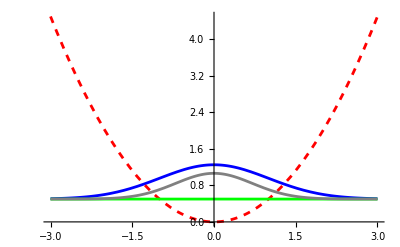
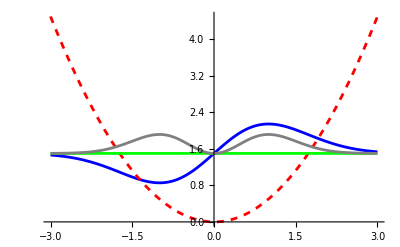
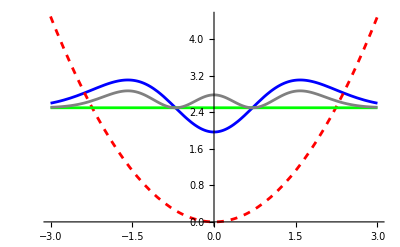
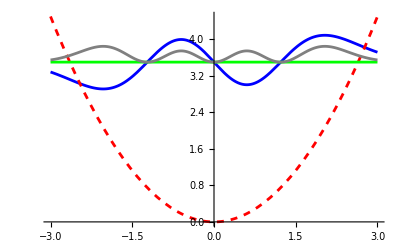
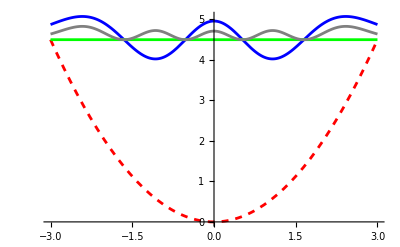
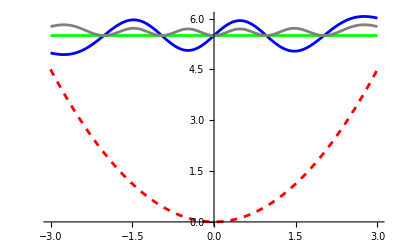
0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-

```mathematica
Table[{n, Plot[{Subscript[ϕ, n][x]+(1/2+n) ℏ ω,1/2 m ω^2 x^2,(1/2+n) ℏ ω, (Subscript[ϕ, n][x])^2+(1/2+n) ℏ ω}/.{m->1,ℏ->1,ω->1}//Evaluate,{x,-3,3},PlotStyle->{Blue,{Red,Dashed},Green,Gray},PlotRange->All]},{n,0,5}]//TableForm
```

### Comparison between LJ-6-12, Morse and HO potentials

```mathematica
vLJ[r_]:=4 ϵ ((a/r)^12-(a/r)^6)
```

```mathematica
rmin =Solve[D[vLJ[r],r]==0,r]
```

{{r→-2^(1/6) a},{r→2^(1/6) a},{r→-(-1)^(1/3) 2^(1/6) a},{r→(-1)^(1/3) 2^(1/6) a},{r→-(-1)^(2/3) 2^(1/6) a},{r→(-1)^(2/3) 2^(1/6) a}}

```mathematica
vLJ[r]/.r->2^(1/6) a
```

-ϵ

What is the strength of this LJ12-6 potential?

```mathematica
D[vLJ[r],{r,2}]/.r->2^(1/6) a
```

(36 2^(2/3) ϵ)/a^2

From the book we have this result:

```mathematica
72/2^(1/3) (ϵ/a^2)//FullSimplify
```

(36 2^(2/3) ϵ)/a^2

```mathematica
(72/2^(1/3) (ϵ/a^2)//FullSimplify) ===(36 2^(2/3) ϵ)/a^2
```

True

### The Morse Potential

```mathematica
vM[r_]:=ϵ (Exp[-2 (r-r0)/b]-2 Exp[-(r-r0)/b])
```

```mathematica
rmin = Solve[D[vM[r],r]==0,r]
```

{{r→ConditionalExpression[r0+2 ⅈ b π C[1], C[1]∈ℤ]}}

```mathematica
vM[r]/.r->r0
```

-ϵ

What is the streght of the potential

```mathematica
D[vM[r],{r,2}]/.r->r0
```

(2 ϵ)/b^2

### HO potential

```mathematica
vHO[r_]:=-ϵ+1/2 m ω^2 (r-r0)^2
```

```mathematica
rmin = Solve[D[vHO[r],r]==0,r]
```

{{r→r0}}

```mathematica
vHO[r]/.r->r0
```

-ϵ

The strength of the potential is

```mathematica
D[vHO[r],{r,2}]/.r->r0
```

m ω^2

Let' s relate the properties of these potentials

```mathematica
Solve[(36 2^(2/3) ϵ)/a^2 == (2 ϵ)/b^2,b]
```

{{b→-a/(3 2^(5/6))},{b→a/(3 2^(5/6))}}

```mathematica
Solve[(36 2^(2/3) ϵ)/a^2 == m ω^2,ω]
```

{{ω→-(6 2^(1/3) √ϵ)/(a √m)},{ω→(6 2^(1/3) √ϵ)/(a √m)}}

Finally, let’s plot the potentials:

```mathematica
Plot[{
Callout[vLJ[r],"vLJ",1.4],
Callout[vM[r],"vM",1.6]/.{b->a/(3 2^(5/6)),r0->2^(1/6) a},
Callout[vHO[r],"vHO",1.]/.{ω->(6 2^(1/3) √ϵ)/(a √m),r0->2^(1/6)a}

}/.{ϵ->1,a->1}//Evaluate,{r,0.8,2}, 
PlotStyle->{Blue,{Yellow,Dashed},Red}, 
PlotRange->{-1.2,1.2},
Frame->True,
FrameLabel->{"r","v(r)"},
AspectRatio->1,
BaseStyle->{FontFamily->"Helvetica",FontSize->15}
]
```

-Graphics-

### Lennard-Jones Potential and the Schrödinger Equation

Defining the potential

```mathematica
vLJ[r_]:=4 ϵ ((a/r)^12-(a/r)^6)
```

```mathematica
eqLJ = (- ℏ^2)/(2 m)ϕ''[r]+vLJ[r] ϕ[r]==ℰ ϕ[r]
```

4 (a^12/r^12-a^6/r^6) ϵ ϕ[r]-(ℏ^2 ϕ''[r])/(2 m)==ℰ ϕ[r]

```mathematica
DSolve[eqLJ,ϕ[r],r]
```

$Aborted

### The Morse Potential and the Schrödinger Equation

```mathematica
vM[r_]:= ϵ (Exp[(-2(r-r0))/b]-2 Exp[(-(r-r0))/b])
```

```mathematica
eqM = -ℏ^2/(2 m) ϕ''[r] + vM[r] ϕ[r] == ℰ  ϕ[r]
```

(ⅇ^(-(2 (r-r0))/b)-2 ⅇ^(-(r-r0)/b)) ϵ ϕ[r]-(ℏ^2 ϕ''[r])/(2 m)==ℰ ϕ[r]

```mathematica
DSolve[eqM,ϕ[r],r]
```

DSolve[(ⅇ^(-(2 (r-r0))/b)-2 ⅇ^(-(r-r0)/b)) ϵ ϕ[r]-(ℏ^2 ϕ''[r])/(2 m)==ℰ ϕ[r],ϕ[r],r]

Let’s change variables:

```mathematica
x->r/b,xe->r0/b
```

We need to check how does transform ∂^2/(∂r^2) ϕ[r]  with those changes of variables:

```mathematica
ImplicitD[ϕ[x], r==b x, x,{r,2}]
```

ϕ''[x]/b^2

```mathematica
(-ℏ^2/(2 m) ImplicitD[ϕ[x], r==b x, x,{r,2}] + vM[r] ϕ[r] == ℰ  ϕ[r]//ExpandAll)/.{r/b->x, r0/b->xe, r->x}//FullSimplify
```

```mathematica
(-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) ϵ ϕ[x]==ℰ ϕ[x]+(ℏ^2 ϕ''[x])/(2 b^2 m)
```

```mathematica
eqM1=(-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) ϵ ϕ[x]==ℰ ϕ[x]+(ℏ^2 ϕ''[x])/(2 b^2 m)
```

(-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) ϵ ϕ[x]==ℰ ϕ[x]+(ℏ^2 ϕ''[x])/(2 b^2 m)

```mathematica
DSolve[eqM1, ϕ[x],x]//FunctionExpand
```

{{ϕ[x]→C[2] [ⅇ^x]+C[1] [ⅇ^x]}}

Now lets simplify more this expression multiplying by (2 mb^2)/ℏ^2

```mathematica
eqM1 * (2 m b^2)/ℏ^2//Apart
```

(2 b^2 m ((-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) ϵ ϕ[x]==ℰ ϕ[x]+(ℏ^2 ϕ''[x])/(2 b^2 m)))/ℏ^2

```mathematica
(eqM1[[1]]* (2 m b^2)/ℏ^2//ExpandAll)==(eqM1[[2]]* (2 m b^2)/ℏ^2//ExpandAll)
```

```mathematica
(2 b^2 (-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) m ϵ ϕ[x])/ℏ^2==(2 b^2 m ℰ ϕ[x])/ℏ^2+ϕ''[x]
```

```mathematica
eqM2 = (2 b^2 (-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) m ϵ ϕ[x])/ℏ^2==(2 b^2 m ℰ ϕ[x])/ℏ^2+ϕ''[x]
```

(2 b^2 (-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) m ϵ ϕ[x])/ℏ^2==(2 b^2 m ℰ ϕ[x])/ℏ^2+ϕ''[x]

let' s define: ℯ is esc + sce + esc

```mathematica
λ^2->(2 b^2 m ϵ)/ℏ^2, ℯ->(2 b^2 m ℰ)/ℏ^2
```

```mathematica
eqM2 = λ^2 (-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) ϕ[x]== ℯ ϕ[x]+ϕ''[x]
```

(-2 ⅇ^(-x+xe)+ⅇ^(-2 x+2 xe)) λ^2 ϕ[x]==ℯ ϕ[x]+ϕ''[x]

```mathematica
DSolve[eqM2, ϕ[x],x]//FunctionExpand
```

{{ϕ[x]→C[2] [ⅇ^x]+C[1] [ⅇ^x]}}

Let' s apply this change of variables

```mathematica
ImplicitD[ϕ[y],y==x-xe,y,{x,2}]
```

ϕ''[y]

then the eqM2 becomes:

```mathematica
λ^2(-2 ⅇ^-y+ⅇ^(-2 y)) ϕ[x]== ℯ ϕ[x]+ϕ''[x]
```

Now let’s define a new change of variable:

```mathematica
(ImplicitD[ϕ[ζ],ζ==2 ⅇ^-y λ^2, ζ,{y,2}]//ExpandAll)
```

2 ⅇ^-y λ^2 ϕ'[ζ]+4 ⅇ^(-2 y) λ^4 ϕ''[ζ]

```mathematica
(ζ^2/(4 λ^2)-ζ) ϕ[ζ] - ℯ ϕ[ζ]-ζ ϕ'[ζ] - ζ^2 ϕ''[ζ]==0//ExpandAll//Collect[#,Derivative[_][ϕ][_],Together]&
```

(ζ^2 ϕ[ζ]-4 ℯ λ^2 ϕ[ζ]-4 ζ λ^2 ϕ[ζ])/(4 λ^2)-ζ ϕ'[ζ]-ζ^2 ϕ''[ζ]==0

```mathematica
eqM3 = (-ℯ -ζ +ζ^2/(4 λ^2))ϕ[ζ]-ζ ϕ'[ζ]-ζ^2 ϕ''[ζ]==0
```

(-ℯ-ζ+ζ^2/(4 λ^2)) ϕ[ζ]-ζ ϕ'[ζ]-ζ^2 ϕ''[ζ]==0

```mathematica
DSolve[eqM3, ϕ[ζ], ζ]//FullSimplify
```

{{ϕ[ζ]→ⅇ^(-ζ/(2 λ)) ζ^(ⅈ √ℯ) (C[1] HypergeometricU[1/2+ⅈ √ℯ-λ,1+2 ⅈ √ℯ,ζ/λ]+C[2] LaguerreL[-1/2-ⅈ √ℯ+λ,2 ⅈ √ℯ,ζ/λ])}}

Let' s analyse the asymptotic behaviour of this solution

```mathematica
Asymptotic[ⅇ^(-ζ/(2 λ)) ζ^(ⅈ √ℯ) HypergeometricU[1/2+ⅈ √ℯ-λ,1+2 ⅈ √ℯ,ζ/λ],ζ->∞]//FullSimplify
```

ⅇ^(-ζ/(2 λ)) ζ^(ⅈ √ℯ) (ζ/λ)^(-1/2-ⅈ √ℯ+λ) (1-((4 ℯ+(1-2 λ)^2) λ)/(4 ζ))

```mathematica
Asymptotic[ⅇ^(-ζ/(2 λ)) ζ^(ⅈ √ℯ) LaguerreL[-1/2-ⅈ √ℯ+λ,2 ⅈ √ℯ,ζ/λ],ζ->∞]//FullSimplify
```

1/(4 π)ⅇ^(-ζ/(2 λ)) ζ^(-1+ⅈ √ℯ) Cosh[π (√ℯ+ⅈ λ)] ((-ζ/λ)^(-1/2-ⅈ √ℯ+λ) (4 ζ-(4 ℯ+(1-2 λ)^2) λ) Gamma[1/2+ⅈ √ℯ-λ]+ⅇ^(ζ/λ) (ζ/λ)^(-1/2-ⅈ √ℯ-λ) (4 ζ+λ (4 ℯ+(1+2 λ)^2)) Gamma[1/2+ⅈ √ℯ+λ])

```mathematica
Solve[Cosh[π (√ℯ+ⅈ λ)]  Gamma[1/2+ⅈ √ℯ-λ]==0,ℯ]//FullSimplify
```

Solve::useq: The answer found by Solve contains equational condition(s) {0==(-(ⅈ π)/2-ⅈ π λ+2 ⅈ π 1-√(-Power[«2»]))/π,0==((ⅈ π)/2-ⅈ π λ+2 ⅈ π 1-√(-Power[«2»]))/π}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

{{ℯ→ConditionalExpression[-1/4 (1-2 λ+4 C[1])^2, ]},{ℯ→ConditionalExpression[-1/4 (1+2 λ-4 C[1])^2, C[1]∈ℤ&&C[1]≤0&&(4 C[1]≥1+λ+Conjugate[λ]||Im[λ]>0)]},{ℯ→ConditionalExpression[-1/4 (1+2 λ-4 C[1])^2, ]},{ℯ→ConditionalExpression[-1/4 (1-2 λ+4 C[1])^2, ]}}

```mathematica
Solve[Cosh[π (√ℯ+ⅈ λ)]  Gamma[1/2+ⅈ √ℯ+λ]==0,ℯ]//FullSimplify
```

Solve::useq: The answer found by Solve contains equational condition(s) {0==(-(ⅈ π)/2-ⅈ π λ+2 ⅈ π 1-√(-Power[«2»]))/π,0==((ⅈ π)/2-ⅈ π λ+2 ⅈ π 1-√(-Power[«2»]))/π}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

{{ℯ→ConditionalExpression[-1/4 (1-2 λ+4 C[1])^2, ]},{ℯ→ConditionalExpression[-1/4 (1+2 λ-4 C[1])^2, ]},{ℯ→ConditionalExpression[-1/4 (1+2 λ-4 C[1])^2, ]},{ℯ→ConditionalExpression[-1/4 (1-2 λ+4 C[1])^2, ]}}

```mathematica
Reduce[1+4 n≥ 2 Re[λ],n]
```

n≥1/4 (-1+2 Re[λ])

```mathematica
Solve[(2 b^2 m ℰ)/ℏ^2==-1/4 (1-2 λ+4 n)^2,ℰ]
```

{{ℰ→-((1+4 n-2 λ)^2 ℏ^2)/(8 b^2 m)}}

```mathematica
ℰM[n_] = -((1+4 n-2 λ)^2 ℏ^2)/(8 b^2 m)/.λ->√((2 b^2 m ϵ)/ℏ^2)//PowerExpand //ExpandAll
```

-ϵ+(√ϵ ℏ)/(√2 b √m)+(2 √2 n √ϵ ℏ)/(b √m)-ℏ^2/(8 b^2 m)-(n ℏ^2)/(b^2 m)-(2 n^2 ℏ^2)/(b^2 m)

```mathematica
ℰM[0]
```

-ϵ+(√ϵ ℏ)/(√2 b √m)-ℏ^2/(8 b^2 m)

And this is the energy of my system

Let' s  consider the Ne_2 molecule

```mathematica
ℰHO[n_]:= -ϵ + (n+1/2) ℏ ω
```

What is the zero point energy (ZPE) of Ne_2according to Morse and HO potentials?

```mathematica
ℰHO[0]
```

-ϵ+(ω ℏ)/2

Let' s estimate for the Morse Potential

```mathematica
(ℰM[0] +ϵ) 10^3/(1.6 10^-19)/.b->a/(3 2^(5/6))/.{ϵ->3.1 10^-3 1.6 10^-19, m->1/2 3.35092 10^-26, ℏ->(6.626 10^-34)/(2 π), a->2.74 10^-10} (*replace with the Ne mass*)
```

1.36701

Let' s estimate for HO potential:

```mathematica
(ℰHO[0] +ϵ) 10^3/(1.6 10^-19)/.ω->(6 2^(1/3)√ϵ)/(a √m)/.{ϵ->3.1 10^-3 1.6 10^-19, m->1/2 3.35092 10^-26, ℏ->(6.626 10^-34)/(2 π), a->2.74 10^-10}
```

1.56437

The Morse potential is more accurate for this kind of system. This molecule a room temperature will never exists.  The dissociation energy is from a lit of bit up of the botton of the pontential since the system will be completely froze in the other case.

The dissociation energy for Ne_2using MOrse potential is:

```mathematica
ℰM[0] 10^3/(1.6 10^-19)/.b->a/(3 2^(5/6))/.{ϵ->3.1 10^-3 1.6 10^-19, m->1/2 3.35092 10^-26, ℏ->(6.626 10^-34)/(2 π), a->2.74 10^-10}
```

-1.73299

Thus the system does exits at room temperature, other wise the system will dissociate.